```mathematica
vert={{-1,-1},{-1,1},{1,1},{1,-1},{-2,-2},{-2,2},{2,2},{2,-2}};
vert1={{-1,-1},{-1,1},{1,1},{1,-1},{-2,-2},{-2,3},{2,3},{2,-2}};
fs={{0,1,4,5},{1,2,5,6},{2,3,6,7},{0,3,4,7},{0,1,2,3}};
es={{0,1},{1,2},{2,3},{0,3},{0,4},{1,5},{2,6},{3,7},{4,5},{5,6},{6,7},{4,7}};
e2=es+1;
V=Join[vert,{{0,0},{-1,2},{-1,-2},{1,2},{1,-2},{-2,1},{-2,-1},{2,1},{2,-1}}];
```

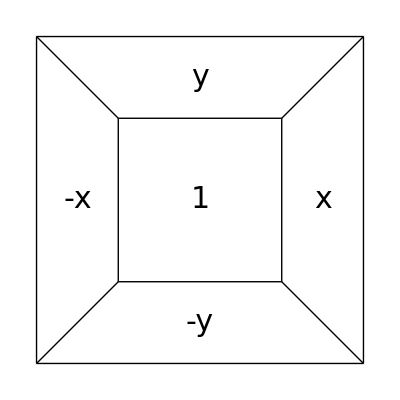

```mathematica
(*ToySplineVertexLabelledC0NonTriv*)
Graphics[Join[{Thick,Black,GraphicsComplex[vert,Line[es+1]]},{(*Text[Style["(-1,-1)",20],{-.7,-1.15}],Text[Style["(1,-1)",20],{.8,-1.15}],
Text[Style["(1,1)",20],{.85,1.15}],
Text[Style["(-1,1)",20],{-.7,1.15}],
Text[Style["(-2,-2)",20],{-2,-2.15}],
Text[Style["(2,-2)",20],{2,-2.15}],
Text[Style["(2,2)",20],{2,2.15}],
Text[Style["(-2,2)",20],{-2,2.15}],*)
Text[Style["-x",30],{-1.5,0}],Text[Style["y",30],{0,1.5}],Text[Style["x",30],{1.5,0}],Text[Style["-y",30],{0,-1.5}],Text[Style["1",30],{0,0}]}]]
```

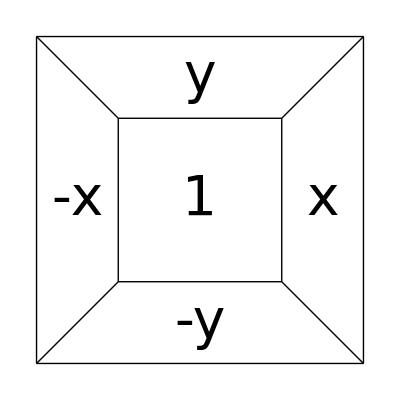

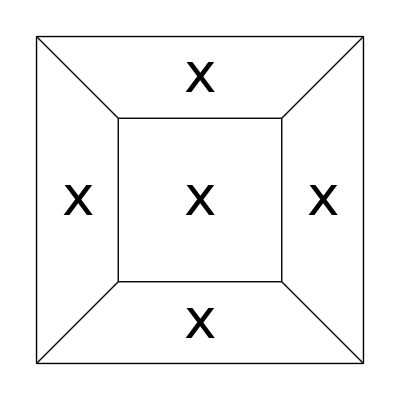

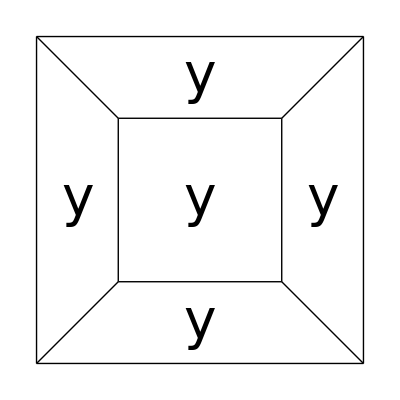

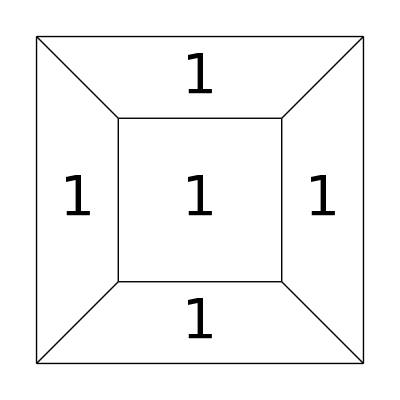

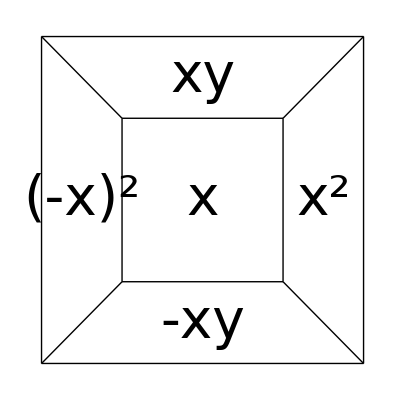

```mathematica
(*ToySplinesVertexNotLabelled*)
TS=55;
Graphics[Join[{Thick,Black,GraphicsComplex[vert,Line[es+1]]},{Text[Style["-x",TS],{-1.5,0}],Text[Style["y",TS],{0,1.5}],Text[Style["x",TS],{1.5,0}],Text[Style["-y",TS],{0,-1.5}],Text[Style["1",TS],{0,0}]}]]
Graphics[Join[{Thick,Black,GraphicsComplex[vert,Line[es+1]]},{
Text[Style["x",TS],{-1.5,0}],Text[Style["x",TS],{0,1.5}],Text[Style["x",TS],{1.5,0}],Text[Style["x",TS],{0,-1.5}],Text[Style["x",TS],{0,0}]}]]
Graphics[Join[{Thick,Black,GraphicsComplex[vert,Line[es+1]]},{
Text[Style["y",TS],{-1.5,0}],Text[Style["y",TS],{0,1.5}],Text[Style["y",TS],{1.5,0}],Text[Style["y",TS],{0,-1.5}],Text[Style["y",TS],{0,0}]}]]
Graphics[Join[{Thick,Black,GraphicsComplex[vert,Line[es+1]]},{
Text[Style["1",TS],{-1.5,0}],Text[Style["1",TS],{0,1.5}],Text[Style["1",TS],{1.5,0}],Text[Style["1",TS],{0,-1.5}],Text[Style["1",TS],{0,0}]}]]
Graphics[Join[{Thick,Black,GraphicsComplex[vert,Line[es+1]]},{Text[Style[Superscript["-x","2"]//DisplayForm,TS],{-1.5,0}],Text[Style["xy",TS],{0,1.5}],Text[Style[Superscript["x","2"],TS],{1.5,0}],Text[Style["-xy",TS],{0,-1.5}],Text[Style["x",TS],{0,0}]}]]
```

```mathematica
PList=vert[[#1]]&/@MySort[vert,#]&/@(fs+1);
P=Polygon[#]&/@PList;
Colors=Lighter[{Red,Green,Yellow,Blue,Purple}];
Directives={Opacity[.5],Colors[[#]],P[[#]]}&/@{1,2,3,4,5};
```

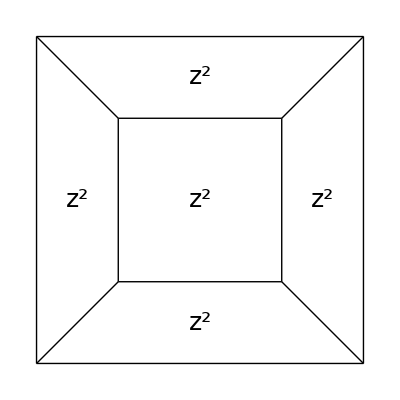

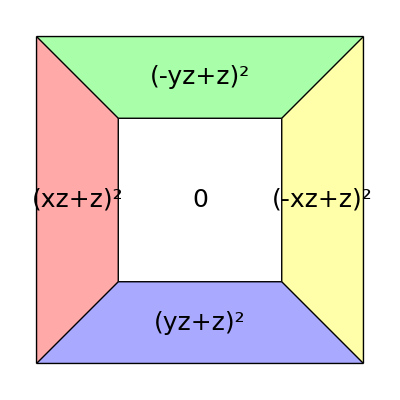

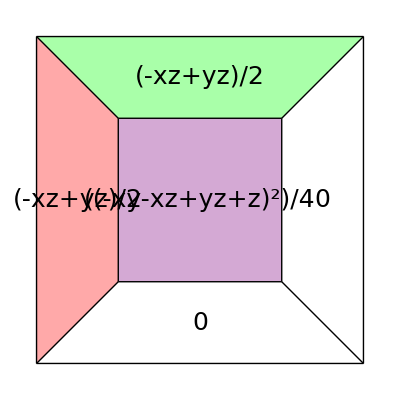

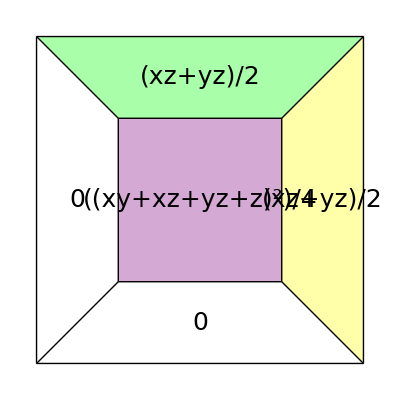

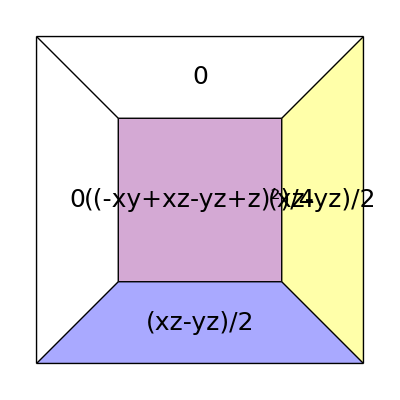

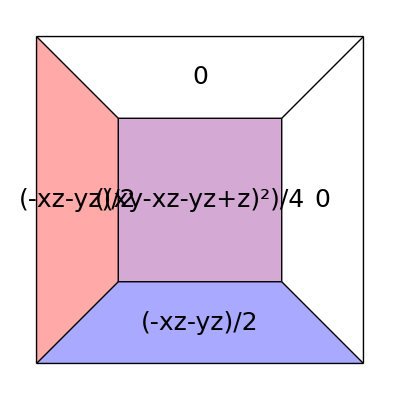

```mathematica
(*Partition of 1*)
TS=25;
Graphics[Join[{Thick,Black,GraphicsComplex[vert,Line[es+1]]},{
Text[Style[Superscript["z","2"],TS],{-1.5,0}],Text[Style[Superscript["z","2"],TS],{0,1.5}],Text[Style[Superscript["z","2"],TS],{1.5,0}],Text[Style[Superscript["z","2"],TS],{0,-1.5}],Text[Style[Superscript["z","2"],TS],{0,0}]}]]
Graphics[Join[Directives[[{1,2,3,4}]],{Thick,Black,GraphicsComplex[vert,Line[es+1]]},{Text[Style[("xz+z")^("2"),TS],{-1.5,0}],Text[Style[("-yz+z")^("2"),TS],{0,1.5}],Text[Style[("-xz+z")^("2"),TS],{1.5,0}],Text[Style[("yz+z")^("2"),TS],{0,-1.5}],Text[Style["0",TS],{0,0}]}]]
Graphics[Join[Directives[[{1,2,5}]],{Thick,Black,GraphicsComplex[vert,Line[es+1]]},{Text[Style[("-xz+yz")/("2"),TS],{-1.5,0}],Text[Style[("-xz+yz")/("2"),TS],{0,1.5}],Text[Style["0",TS],{1.5,0}],Text[Style["0",TS],{0,-1.5}],Text[Style[("-xy-xz+yz+z")^("2")/("4"),TS],{0,0}]}]]
Graphics[Join[Directives[[{2,3,5}]],{Thick,Black,GraphicsComplex[vert,Line[es+1]]},{Text[Style["0",TS],{-1.5,0}],Text[Style[("xz+yz")/("2"),TS],{0,1.5}],Text[Style[("xz+yz")/("2"),TS],{1.5,0}],Text[Style["0",TS],{0,-1.5}],Text[Style[("xy+xz+yz+z")^("2")/("4"),TS],{0,0}]}]]
Graphics[Join[Directives[[{3,4,5}]],{Thick,Black,GraphicsComplex[vert,Line[es+1]]},{Text[Style["0",TS],{-1.5,0}],Text[Style["0",TS],{0,1.5}],Text[Style[("xz-yz")/("2"),TS],{1.5,0}],Text[Style[("xz-yz")/("2"),TS],{0,-1.5}],Text[Style[("-xy+xz-yz+z")^("2")/("4"),TS],{0,0}]}]]
Graphics[Join[Directives[[{1,4,5}]],{Thick,Black,GraphicsComplex[vert,Line[es+1]]},{Text[Style[("-xz-yz")/("2"),TS],{-1.5,0}],Text[Style["0",TS],{0,1.5}],Text[Style["0",TS],{1.5,0}],Text[Style[("-xz-yz")/("2"),TS],{0,-1.5}],Text[Style[("xy-xz-yz+z")^("2")/("4"),TS],{0,0}]}]]
```

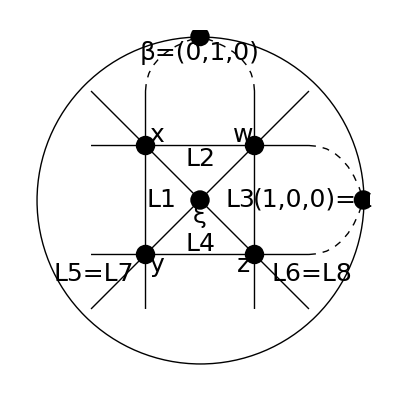

```mathematica
(*Projective Hyperlplane Arrangement*)
Graphics[{GraphicsComplex[Join[V,{{0,3},{3,0}}],{Thick,Circle[{0,0},3],Line[{{5,7},{6,8},{15,17},{14,16},{10,11},{12,13}}],PointSize[.035],Point[{1,2,3,4,9,18,19}],
Text[Style["L1",25],{-.7,0}],
Text[Style["L2",25],{0,.75}],
Text[Style["L3",25],{.75,0}],
Text[Style["L4",25],{0,-.8}],Text[Style["y",25],{-.8,-1.2}],Text[Style["z",25],{.8,-1.2}],
Text[Style["w",25],{.8,1.2}],
Text[Style["x",25],{-.8,1.2}],
Text[Style["ξ",25],{0,-.3}],
Text[Style["L5=L7",25],{-1.95,-1.35}],
Text[Style["L6=L8",25],{2.05,-1.35}],
Text[Style["β=(0,1,0)",25],{0,2.7}],
Text[Style["(1,0,0)=α",25],{2.08,0}]}],Thick,Dashed,BezierCurve[{{2,1},{2.7,1},{3,0}}],Dashed,BezierCurve[{{2,-1},{2.7,-1},{3,0}}],Dashed,BezierCurve[{{-1,2},{-1,2.7},{0,3}}],Dashed,BezierCurve[{{1,2},{1,2.7},{0,3}}]}]
```

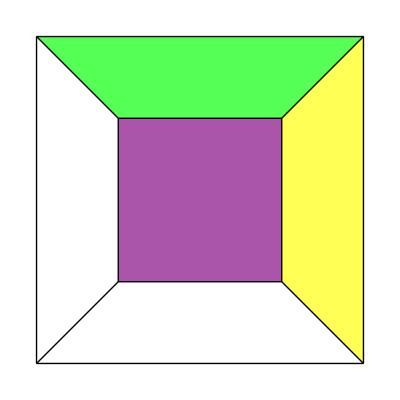

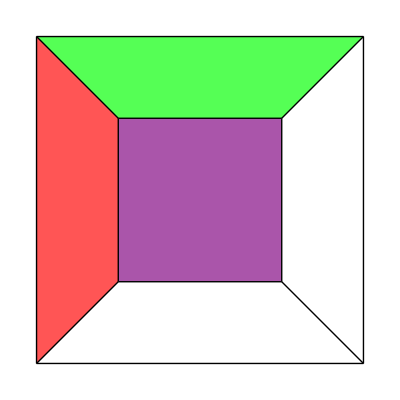

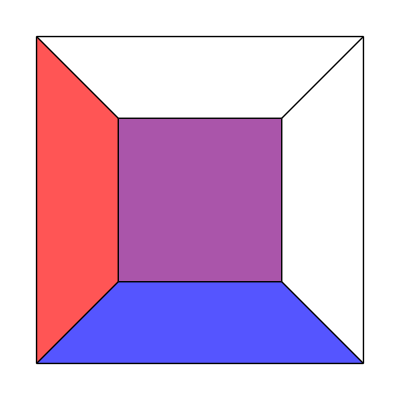

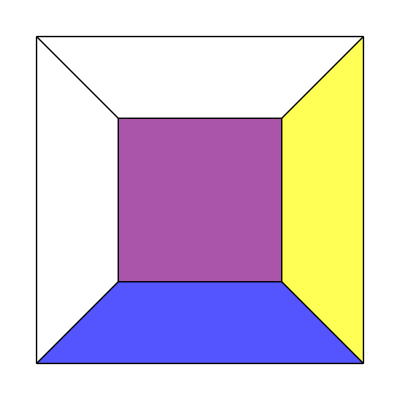

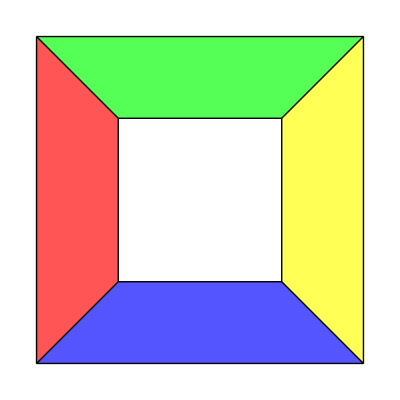

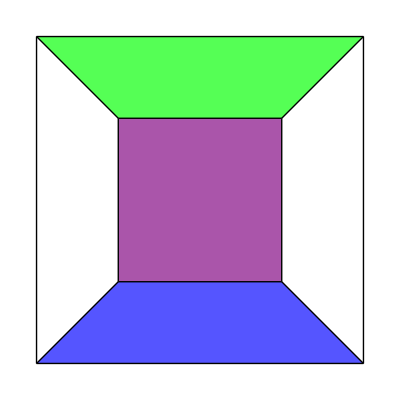

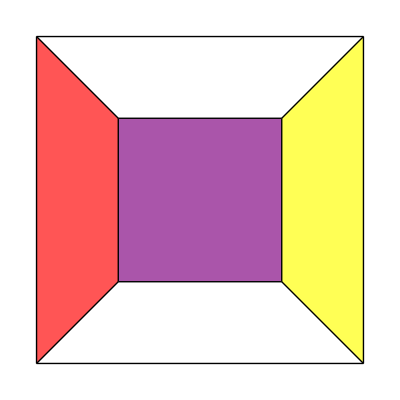

```mathematica
(*Unlabelled Star of W*)
Graphics[Join[Directives[[{2,3,5}]],{Thick,Black,GraphicsComplex[vert,Line[es+1]]}]]
(*Unlabelled Star of X*)
Graphics[Join[Directives[[{1,2,5}]],{Thick,Black,GraphicsComplex[vert,Line[es+1]]}]]
(*Unlabelled Star of Y*)
Graphics[Join[Directives[[{1,4,5}]],{Thick,Black,GraphicsComplex[vert,Line[es+1]]}]]
(*Unlabelled Star of Z*)
Graphics[Join[Directives[[{3,4,5}]],{Thick,Black,GraphicsComplex[vert,Line[es+1]]}]]
(*Unlabelled \QC_\xi *)
Graphics[Join[Directives[[{1,2,3,4}]],{Thick,Black,GraphicsComplex[vert,Line[es+1]]}]]
(*Unlabelled \QC_\alpha *)
Graphics[Join[Directives[[{2,4,5}]],{Thick,Black,GraphicsComplex[vert,Line[es+1]]}]]
(*Unlabelled \QC_\beta *)
Graphics[Join[Directives[[{1,3,5}]],{Thick,Black,GraphicsComplex[vert,Line[es+1]]}]]
```

```mathematica
{{1,-1,0,0,0,x-y,0,0,0,0,0,0,0},{0,1,-1,0,0,0,x+y,0,0,0,0,0,0},
{0,0,1,-1,0,0,0,x-y,0,0,0,0,0},
{-1,0,0,1,0,0,0,0,x+y,0,0,0,0},
{1,0,0,0,-1,0,0,0,0,x+1,0,0,0},
{0,1,0,0,-1,0,0,0,0,0,y-1,0,0},
{0,0,1,0,-1,0,0,0,0,0,0,x-1,0},
{0,0,0,1,-1,0,0,0,0,0,0,0,x+y}}//MatrixForm
```

(1 | -1 | 0 | 0 | 0 | x-y | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -1 | 0 | 0 | 0 | x+y | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -1 | 0 | 0 | 0 | x-y | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | x+y | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1+x | 0 | 0 | 0
0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1+y | 0 | 0
0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1+x | 0
0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x+y)